```mathematica
ClearAll["Global`*"]
```

## Constant height test

```mathematica
g=9.80655;
m=.056+1.518;
```

```mathematica
a[α_,β_,γ_]:={g*m*Sec[β]*Sec[γ]*(Cos[α]*Cos[γ]*Sin[β]+Sin[α]*Sin[γ]),g*m*Sec[β]*Sec[γ]*(Cos[γ]*Sin[α]*Sin[β]-Cos[α]*Sin[γ]),0}/m
```

```mathematica
(*soln=NDSolve[{r''[t]==a[0,0,Pi/6],
r[0]=={0,0,0},
r'[0]=={0,0,0}},r[t],{t,0,1.0}]
rsol[t_]=soln[[1,1,2]]
ParametricPlot3D[{rsol[t]rsol'[t]},{t,0,1.0}]*)
```

```mathematica
t0=0;
dt=1/20;
table={};
vtable={};
rtable={};
For[α=0,α<π/2,α=α+π/6,
For[β=0,β<π/2,β=β+π/6,
For[γ=0,γ<π/2,γ=γ+π/6,
soln=NDSolve[{r''[s]==a[α,β,γ],
r[0]=={0,0,0},
r'[0]=={0,0,0}},r[s],{s,0,1.0}];
rsol[s_]=soln[[1,1,2]];
For[t=0,t<1.0,t=t+dt,
(*Print[{α,β,γ,N[t]}];*)
rfunc[s_]=Integrate[a[α,β,γ],s,s];
rint=rfunc[t];
AppendTo[rtable,{t,rint[[3]]}];
(*Print[r];*)
vfunc[s_]=Integrate[a[α,β,γ],s];
vint=vfunc[t];
AppendTo[vtable,{N[t],vint[[3]]}];
AppendTo[table,{α,β,γ,N[t],vint,rsol'[t],rint,rsol[t]}]
]
]
]
]
```

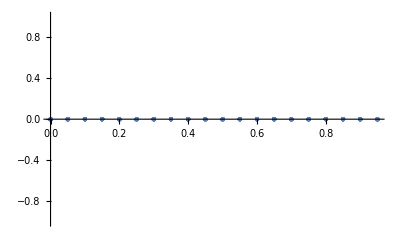

```mathematica
ListPlot[rtable]
PaddedForm[TableForm[table],{2,1}];
```